```mathematica
f[d_,r_] := ArcCos[d/r]/Pi * 2*Pi*r*E^(-Pi*r^2)
p[d_] := NIntegrate[f[d,r],{r,d,Infinity}]
```

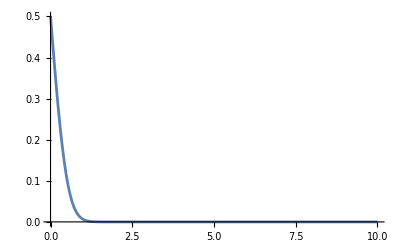

```mathematica
Plot[p[d],{d,0,10},PlotRange -> Full]
```